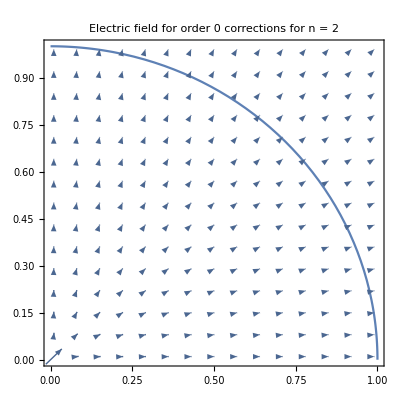

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=0;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=1;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00289566-0.00261156 ⅈ and 0.0321842 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00268136-0.00275104 ⅈ and 0.0308052 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0000271858-0.0012419 ⅈ and 0.0117396 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

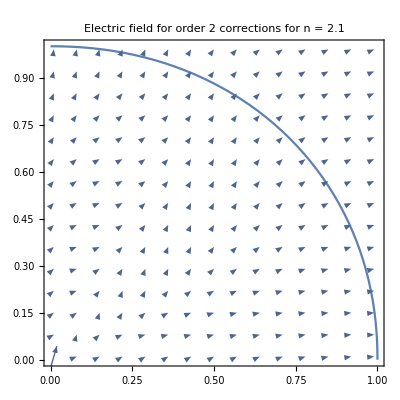

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=2.1;(* Exponents of x^n+y^n=R^n*)
R=1;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00276234-0.00213816 ⅈ and 0.0265837 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00272524-0.00294286 ⅈ and 0.032738 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0000160785-0.00216328 ⅈ and 0.0208389 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

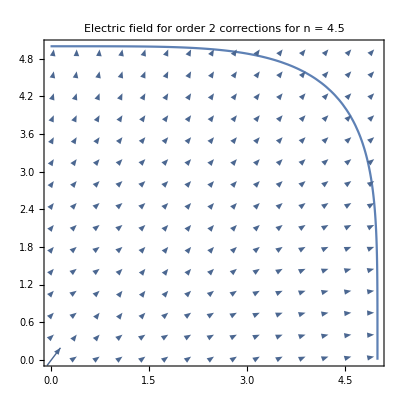

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=4.5;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273835-0.00213929 ⅈ and 0.025577 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273623-0.00294245 ⅈ and 0.0337777 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 4.7484×10^-6-0.00215255 ⅈ and 0.0197751 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

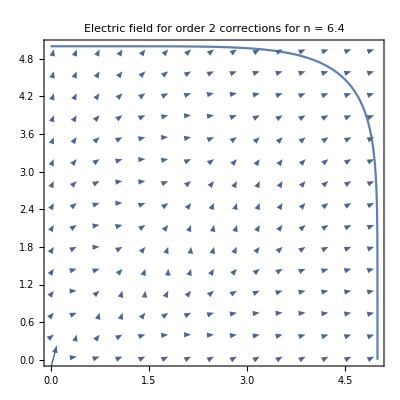

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=6.4;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.81714×10^-6-0.00129858 ⅈ and 0.0461384 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.47208×10^-6-0.00244462 ⅈ and 0.0652463 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 4.98012×10^-6-0.00183743 ⅈ and 0.0280777 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

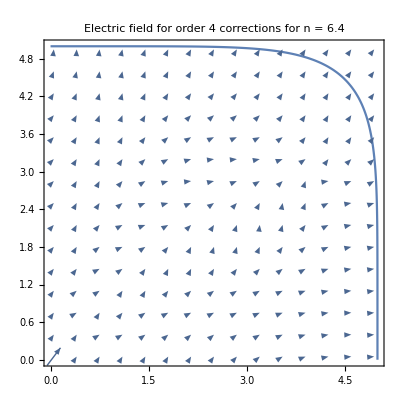

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=6.4;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273372-0.00213818 ⅈ and 0.0226177 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273835-0.00294296 ⅈ and 0.03069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 3.03676×10^-6-0.00215074 ⅈ and 0.0191054 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

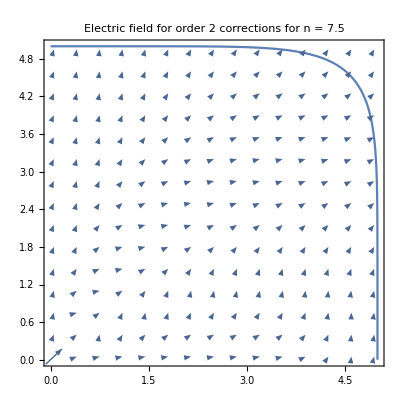

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=2;(* Half the number of coefficients Am or Bm *)
n=7.5;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.15506×10^-6-0.00129912 ⅈ and 0.0416486 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 9.36224×10^-6-0.002444 ⅈ and 0.0707963 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 2.66582×10^-6-0.00183651 ⅈ and 0.0291914 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

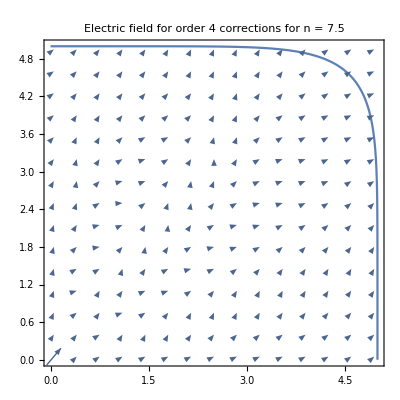

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=4;(* Half the number of coefficients Am or Bm *)
n=7.5;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -8.95733×10^-7-0.000650178 ⅈ and 0.0385299 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.0000101035-0.00223867 ⅈ and 0.0552469 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 1.15506×10^-6-0.00129912 ⅈ and 0.0416486 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

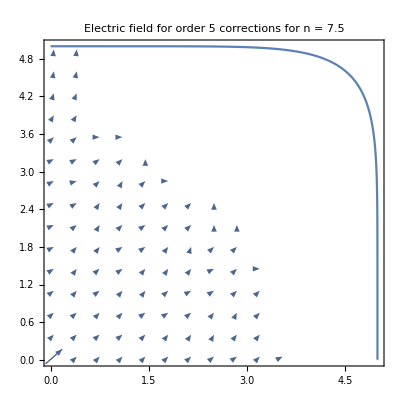

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=5;(* Half the number of coefficients Am or Bm *)
n=7.5;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00214589+6.82316×10^-6 ⅈ and 0.0208095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 5.60365×10^-6+1.84414×10^-6 ⅈ and 0.0963986 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -8.95733×10^-7-0.000650178 ⅈ and 0.0385299 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

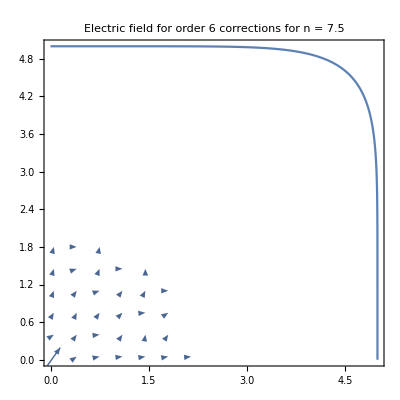

```mathematica
Block[
{M,kMax,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et},
M=6;(* Half the number of coefficients Am or Bm *)
n=7.5;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ib[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ic[k_]:=NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Id[m_,k_]:=NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
Ie[m_,k_]:=NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[m,k]+m B[m]/R^(m+1) Ib[m,k],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[m,k]+B[m]/R^m Ie[m,k],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
soln=NSolve[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```